Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

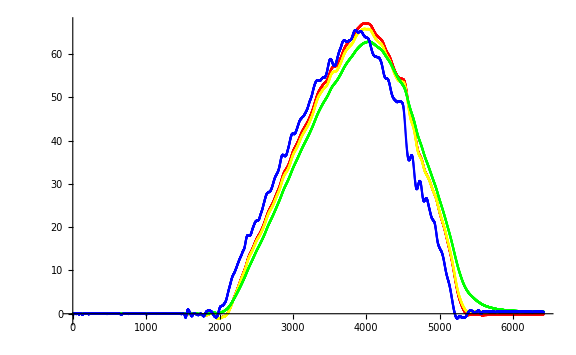

```mathematica
data =Import[FileNameJoin[{NotebookDirectory[],"log"}],"Table","FieldSeparators"->" "];
SetOptions[ListPlot,ImageSize->Large];

accelX[n_]:=data[[n,1]];
accelY[n_]:=data[[n,2]];
accelZ[n_]:=data[[n,3]];
gyroX[n_]:=data[[n,4]];
gyroY[n_]:=data[[n,5]];
gyroZ[n_]:=data[[n,6]];
normAccel[n_]:=Normalize[{data[[n,1]],data[[n,2]],data[[n,3]]}];

complementaryRoll[coeff_]:=RecurrenceTable[{
euler[n+1]==coeff*(euler[n]+gyroY[n]*0.001)+(1-coeff)*(ArcTan[accelZ[n],accelY[n]]/Degree),
euler[1]==0},
euler,{n,1,Length[data]}];

mahonyRoll2[kp_,ki_]:=Module[{Kp=kp,Ki=ki,quaternion={1,0,0,0},mahonyIntegral={0,0,0},mahonyRoll={}},

Do[{
gyroRad={gyroX[n]Degree,gyroY[n]Degree,gyroZ[n]Degree};
halfV={quaternion[[2]]*quaternion[[4]]-quaternion[[1]]*quaternion[[3]],quaternion[[1]]*quaternion[[2]]+quaternion[[3]]*quaternion[[4]],quaternion[[1]]^2-0.5+quaternion[[4]]^2};
halfE={normAccel[n][[2]]*halfV[[3]]-normAccel[n][[3]]*halfV[[2]],normAccel[n][[3]]*halfV[[1]]-normAccel[n][[1]]*halfV[[3]],normAccel[n][[1]]*halfV[[2]]-normAccel[n][[2]]*halfV[[1]]};

mahonyIntegral=mahonyIntegral+2*Ki*halfE*0.001;
gyroRad=gyroRad+mahonyIntegral;

gyroRad=gyroRad+2*Kp*halfE;
gyroRad=gyroRad*0.5*0.001;
qa=quaternion[[1]];qb=quaternion[[2]];qc=quaternion[[3]];
quaternion[[1]]=quaternion[[1]]+(-qb*gyroRad[[1]]-qc*gyroRad[[2]]-quaternion[[4]]*gyroRad[[3]]);
quaternion[[2]]=quaternion[[2]]+(qa*gyroRad[[1]]+qc*gyroRad[[3]]-quaternion[[4]]*gyroRad[[2]]);
quaternion[[3]]=quaternion[[3]]+(qa*gyroRad[[2]]-qb*gyroRad[[3]]+quaternion[[4]]*gyroRad[[1]]);
quaternion[[4]]=quaternion[[4]]+(qa*gyroRad[[3]]+qb*gyroRad[[2]]-qc*gyroRad[[1]]);

quaternion=Normalize[quaternion];

t0=2*(quaternion[[1]]*quaternion[[2]]+quaternion[[3]]*quaternion[[4]]);
t1=1-2*(quaternion[[2]]^2+quaternion[[3]]^2);

mahonyRoll=Append[mahonyRoll,ArcTan[t1,t0]/Degree];

},{n,1,Length[data]}];mahonyRoll]

ListPlot[{mahonyRoll2[50,4],mahonyRoll2[20,1],complementaryRoll[0.9],complementaryRoll[0.0000001]},PlotStyle->{Red,Yellow,Green,Blue}]
```